```mathematica
(* LOAD VARIABLES ----------------------
loads all functions and data (made in this file and evaluated previously) into memory so you don't have to run them again *)
Get[StringReplace[NotebookFileName[],".nb"->", variables.mx"]];
```

Get::noopen: Cannot open TraditionalForm`"C:\\Users\\Omar\\Dropbox\\Academic\\Projects\\9. LHV models for N Qubit Werner State\\Code\\3.Three Qubit Werner State, variables.mx".

```mathematica
(* SAVE VARIABLES ----------------
Save the variables after evaluating them initially so you don't have to re-evaluate them every time *)
DumpSave[StringReplace[NotebookFileName[],".nb"->", variables.mx"],"Global`"];
```

```mathematica
AppendTo[$Path,ToFileName[{$HomeDirectory,"Dropbox","Academic","Code"}]];
<<BlochSVD`
```

```mathematica
comm[x_,y_]:=x.y-y.x
```

```mathematica
acomm[x_,y_]:=x.y+y.x
```

```mathematica
pf={{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
tPauliBasis3=Table[KroneckerProduct[pf[[i]],pf[[j]],pf[[k]]],{i,4},{j,4},{k,4}];
```

```mathematica
viewVec={3.25,-2.5,.25};
```

```mathematica
(* play around with tripartite Werner states, in terms of isotropic tensors, Levi Civita and Kronecker Delta*)
```

```mathematica
mMixed=ConstantArray[0,{4,4,4}]; mMixed[[1,1,1]]=1;
```

```mathematica
xyz=xy=yz=zx=mMixed;
```

```mathematica
xyz[[2;;4,2;;4,2;;4]]=LeviCivitaTensor[3]
```

SparseArray[<6>, {3, 3, 3}]

```mathematica
xy[[2;;4,2;;4,1]]=IdentityMatrix[3];
```

```mathematica
yz[[1,2;;4,2;;4]]=IdentityMatrix[3];
```

```mathematica
zx[[2;;4,1,2;;4]]=IdentityMatrix[3];
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
BlochTensor3=Simplify[mMixed(1-a-b-c-d)+a xy +b yz +c zx +d xyz]
```

({1,0,0,0} | {0,b,0,0} | {0,0,b,0} | {0,0,0,b}
{0,c,0,0} | {a,0,0,0} | {0,0,0,d} | {0,0,-d,0}
{0,0,c,0} | {0,0,0,-d} | {a,0,0,0} | {0,d,0,0}
{0,0,0,c} | {0,0,d,0} | {0,-d,0,0} | {a,0,0,0})

```mathematica
rho = Total[BlochTensor3*tPauliBasis3,3]/8
```

(1/8 (a+b+c+1) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/8 (a-b-c+1) | 1/8 (2 b+2 ⅈ d) | 0 | 1/8 (2 c-2 ⅈ d) | 0 | 0 | 0
0 | 1/8 (2 b-2 ⅈ d) | 1/8 (-a-b+c+1) | 0 | 1/8 (2 a+2 ⅈ d) | 0 | 0 | 0
0 | 0 | 0 | 1/8 (-a+b-c+1) | 0 | 1/8 (2 a-2 ⅈ d) | 1/8 (2 c+2 ⅈ d) | 0
0 | 1/8 (2 c+2 ⅈ d) | 1/8 (2 a-2 ⅈ d) | 0 | 1/8 (-a+b-c+1) | 0 | 0 | 0
0 | 0 | 0 | 1/8 (2 a+2 ⅈ d) | 0 | 1/8 (-a-b+c+1) | 1/8 (2 b-2 ⅈ d) | 0
0 | 0 | 0 | 1/8 (2 c-2 ⅈ d) | 0 | 1/8 (2 b+2 ⅈ d) | 1/8 (a-b-c+1) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 (a+b+c+1))

```mathematica
(* Purity *)
pur=Simplify[Tr[rho.rho]]
```

1/8 (3 a^2+3 b^2+3 c^2+6 d^2+1)

```mathematica
(* {a->-1/3,b->-1/3,c->-1/3,d->1/√3} is extremal, as is {a->1/3,b->1/3,c->1/3,d->0} *)
```

```mathematica
pur/.{a->-1/3,b->-1/3,c->-1/3,d->1/√3}
```

1/2

```mathematica
eigenvalues=Eigenvalues[rho]
```

{1/8 (a+b+c+1),1/8 (a+b+c+1),1/8 (a+b+c+1),1/8 (a+b+c+1),1/8 (-2 √(a^2-a b-a c+b^2-b c+c^2+3 d^2)-a-b-c+1),1/8 (-2 √(a^2-a b-a c+b^2-b c+c^2+3 d^2)-a-b-c+1),1/8 (2 √(a^2-a b-a c+b^2-b c+c^2+3 d^2)-a-b-c+1),1/8 (2 √(a^2-a b-a c+b^2-b c+c^2+3 d^2)-a-b-c+1)}

```mathematica
eigenvalues/.{a->0,b->0,c->0,d-> 1/(2 √3)}
```

{1/8,1/8,1/8,1/8,0,0,1/4,1/4}

```mathematica
(* test projections *)
vec={v1,v2,v3,v4,v5,v6,v7,v8};
```

```mathematica
proj=rho2r[KroneckerProduct[vec,vec]]
```

({v1^2+v2^2+v3^2+v4^2+v5^2+v6^2+v7^2+v8^2,2 v1 v2+2 v3 v4+2 v5 v6+2 v7 v8,0,v1^2-v2^2+v3^2-v4^2+v5^2-v6^2+v7^2-v8^2} | {2 v1 v3+2 v2 v4+2 v5 v7+2 v6 v8,2 v2 v3+2 v1 v4+2 v6 v7+2 v5 v8,0,2 v1 v3-2 v2 v4+2 v5 v7-2 v6 v8} | {0,0,2 v2 v3-2 v1 v4+2 v6 v7-2 v5 v8,0} | {v1^2+v2^2-v3^2-v4^2+v5^2+v6^2-v7^2-v8^2,2 v1 v2-2 v3 v4+2 v5 v6-2 v7 v8,0,v1^2-v2^2-v3^2+v4^2+v5^2-v6^2-v7^2+v8^2}
{2 v1 v5+2 v2 v6+2 v3 v7+2 v4 v8,2 v2 v5+2 v1 v6+2 v4 v7+2 v3 v8,0,2 v1 v5-2 v2 v6+2 v3 v7-2 v4 v8} | {2 v3 v5+2 v4 v6+2 v1 v7+2 v2 v8,2 v4 v5+2 v3 v6+2 v2 v7+2 v1 v8,0,2 v3 v5-2 v4 v6+2 v1 v7-2 v2 v8} | {0,0,-2 v4 v5+2 v3 v6+2 v2 v7-2 v1 v8,0} | {2 v1 v5+2 v2 v6-2 v3 v7-2 v4 v8,2 v2 v5+2 v1 v6-2 v4 v7-2 v3 v8,0,2 v1 v5-2 v2 v6-2 v3 v7+2 v4 v8}
{0,0,2 v2 v5-2 v1 v6+2 v4 v7-2 v3 v8,0} | {0,0,2 v4 v5-2 v3 v6+2 v2 v7-2 v1 v8,0} | {2 v3 v5+2 v4 v6-2 v1 v7-2 v2 v8,2 v4 v5+2 v3 v6-2 v2 v7-2 v1 v8,0,2 v3 v5-2 v4 v6-2 v1 v7+2 v2 v8} | {0,0,2 v2 v5-2 v1 v6-2 v4 v7+2 v3 v8,0}
{v1^2+v2^2+v3^2+v4^2-v5^2-v6^2-v7^2-v8^2,2 v1 v2+2 v3 v4-2 v5 v6-2 v7 v8,0,v1^2-v2^2+v3^2-v4^2-v5^2+v6^2-v7^2+v8^2} | {2 v1 v3+2 v2 v4-2 v5 v7-2 v6 v8,2 v2 v3+2 v1 v4-2 v6 v7-2 v5 v8,0,2 v1 v3-2 v2 v4-2 v5 v7+2 v6 v8} | {0,0,2 v2 v3-2 v1 v4-2 v6 v7+2 v5 v8,0} | {v1^2+v2^2-v3^2-v4^2-v5^2-v6^2+v7^2+v8^2,2 v1 v2-2 v3 v4-2 v5 v6+2 v7 v8,0,v1^2-v2^2-v3^2+v4^2-v5^2+v6^2+v7^2-v8^2})

```mathematica
Manipulate[Quiet[Module[{positivity,purity},
positivity=ContourPlot3D[a+b+c+2Sqrt[a^2+b^2+c^2-a c -a b-b c+3d^2]== 1 ,{a,-1,1},{b,-1,1},{c,-1,1},PlotPoints->10,RegionFunction-> Function[{a,b,c },1+a+b+c≥ 0 ]];
purity=ContourPlot3D[1/8 (3 a^2+3 b^2+3 c^2+6 d^2+1)== 1/2 ,{a,-1,1},{b,-1,1},{c,-1,1},PlotPoints->10,ContourStyle->Directive[Red,Opacity[0.2]],MeshStyle->Directive[Opacity[0.2]],Mesh-> 3];
Show[positivity,purity,ViewPoint->viewVec]
]],{d,0,1/√3}]
```

```mathematica
(* ------- Rotation matrix ------ *)
av=Normalize[{1,1,1}];
o=Simplify[Cos[α]IdentityMatrix[3]+(1-Cos[α])KroneckerProduct[av,av]+Sin[α](LeviCivitaTensor[3].av)ᵀ]
```

(1/3 (2 cos(α)+1) | 1/3 (-cos(α)-√3 sin(α)+1) | 1/3 (-cos(α)+√3 sin(α)+1)
1/3 (-cos(α)+√3 sin(α)+1) | 1/3 (2 cos(α)+1) | 1/3 (-cos(α)-√3 sin(α)+1)
1/3 (-cos(α)-√3 sin(α)+1) | 1/3 (-cos(α)+√3 sin(α)+1) | 1/3 (2 cos(α)+1))

```mathematica
o.oᵀ==oᵀ.o
```

True

```mathematica
N[(o/.{α-> -Pi/2}).{-1,0,0}]
```

{-0.333333,0.244017,-0.910684}

```mathematica
Simplify[o.oᵀ]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Solve[a+b+c+2Sqrt[a^2+b^2+c^2-a c -a b-b c+1]== 1,{a,b,c}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→1/3 (-2 √(9 a b-3 a-3 b-2)+3 a+3 b-1)},{c→1/3 (2 √(9 a b-3 a-3 b-2)+3 a+3 b-1)}}

```mathematica
(*---- try general tensor --- *)
```

```mathematica
Array[W,{3,3,3}]
```

({W(1,1,1),W(1,1,2),W(1,1,3)} | {W(1,2,1),W(1,2,2),W(1,2,3)} | {W(1,3,1),W(1,3,2),W(1,3,3)}
{W(2,1,1),W(2,1,2),W(2,1,3)} | {W(2,2,1),W(2,2,2),W(2,2,3)} | {W(2,3,1),W(2,3,2),W(2,3,3)}
{W(3,1,1),W(3,1,2),W(3,1,3)} | {W(3,2,1),W(3,2,2),W(3,2,3)} | {W(3,3,1),W(3,3,2),W(3,3,3)})

```mathematica
Clear[W]
```

```mathematica
a=Array[temp,{4,4,4},{0,0,0}];
```

```mathematica
a[[2;;4,2;;4,2;;4]]=Array[W,{3,3,3}];
```

```mathematica
a[[2;;4,2;;4,1]]=Array[Y,{3,3}];
```

```mathematica
a[[2;;4,1,2;;4]]=Array[M,{3,3}];
```

```mathematica
a[[1,2;;4,2;;4]]=Array[C,{3,3}];
```

```mathematica
a[[1,1,2;;4]]=Array[b,3];
```

```mathematica
a[[1,2;;4,1]]=Array[g,3,1];
```

```mathematica
a[[2;;4,1,1]]=Array[r,3];
```

```mathematica
a[[1,1,1]]=1;
```

```mathematica
a
```

({1,b(1),b(2),b(3)} | {g(1),C[1,1],C[1,2],C[1,3]} | {g(2),C[2,1],C[2,2],C[2,3]} | {g(3),C[3,1],C[3,2],C[3,3]}
{r(1),M(1,1),M(1,2),M(1,3)} | {Y(1,1),W(1,1,1),W(1,1,2),W(1,1,3)} | {Y(1,2),W(1,2,1),W(1,2,2),W(1,2,3)} | {Y(1,3),W(1,3,1),W(1,3,2),W(1,3,3)}
{r(2),M(2,1),M(2,2),M(2,3)} | {Y(2,1),W(2,1,1),W(2,1,2),W(2,1,3)} | {Y(2,2),W(2,2,1),W(2,2,2),W(2,2,3)} | {Y(2,3),W(2,3,1),W(2,3,2),W(2,3,3)}
{r(3),M(3,1),M(3,2),M(3,3)} | {Y(3,1),W(3,1,1),W(3,1,2),W(3,1,3)} | {Y(3,2),W(3,2,1),W(3,2,2),W(3,2,3)} | {Y(3,3),W(3,3,1),W(3,3,2),W(3,3,3)})

```mathematica
ρ= r2rho[a]
```

(1/8 (b(3)+C[3,3]+g(3)+M(3,3)+r(3)+W(3,3,3)+Y(3,3)+1) | 1/8 (b(1)-ⅈ b(2)+C[3,1]-ⅈ C[3,2]+M(3,1)-ⅈ M(3,2)+W(3,3,1)-ⅈ W(3,3,2)) | 1/8 (C[1,3]-ⅈ C[2,3]+g(1)-ⅈ g(2)+W(3,1,3)-ⅈ W(3,2,3)+Y(3,1)-ⅈ Y(3,2)) | 1/8 (C[1,1]-ⅈ C[1,2]-ⅈ C[2,1]-C[2,2]+W(3,1,1)-ⅈ W(3,1,2)-ⅈ W(3,2,1)-W(3,2,2)) | 1/8 (M(1,3)-ⅈ M(2,3)+r(1)-ⅈ r(2)+W(1,3,3)-ⅈ W(2,3,3)+Y(1,3)-ⅈ Y(2,3)) | 1/8 (M(1,1)-ⅈ M(1,2)-ⅈ M(2,1)-M(2,2)+W(1,3,1)-ⅈ W(1,3,2)-ⅈ W(2,3,1)-W(2,3,2)) | 1/8 (W(1,1,3)-ⅈ W(1,2,3)-ⅈ W(2,1,3)-W(2,2,3)+Y(1,1)-ⅈ Y(1,2)-ⅈ Y(2,1)-Y(2,2)) | 1/8 (W(1,1,1)-ⅈ W(1,1,2)-ⅈ W(1,2,1)-W(1,2,2)-ⅈ W(2,1,1)-W(2,1,2)-W(2,2,1)+ⅈ W(2,2,2))
1/8 (b(1)+ⅈ b(2)+C[3,1]+ⅈ C[3,2]+M(3,1)+ⅈ M(3,2)+W(3,3,1)+ⅈ W(3,3,2)) | 1/8 (-b(3)-C[3,3]+g(3)-M(3,3)+r(3)-W(3,3,3)+Y(3,3)+1) | 1/8 (C[1,1]+ⅈ C[1,2]-ⅈ C[2,1]+C[2,2]+W(3,1,1)+ⅈ W(3,1,2)-ⅈ W(3,2,1)+W(3,2,2)) | 1/8 (-C[1,3]+ⅈ C[2,3]+g(1)-ⅈ g(2)-W(3,1,3)+ⅈ W(3,2,3)+Y(3,1)-ⅈ Y(3,2)) | 1/8 (M(1,1)+ⅈ M(1,2)-ⅈ M(2,1)+M(2,2)+W(1,3,1)+ⅈ W(1,3,2)-ⅈ W(2,3,1)+W(2,3,2)) | 1/8 (-M(1,3)+ⅈ M(2,3)+r(1)-ⅈ r(2)-W(1,3,3)+ⅈ W(2,3,3)+Y(1,3)-ⅈ Y(2,3)) | 1/8 (W(1,1,1)+ⅈ W(1,1,2)-ⅈ W(1,2,1)+W(1,2,2)-ⅈ W(2,1,1)+W(2,1,2)-W(2,2,1)-ⅈ W(2,2,2)) | 1/8 (-W(1,1,3)+ⅈ W(1,2,3)+ⅈ W(2,1,3)+W(2,2,3)+Y(1,1)-ⅈ Y(1,2)-ⅈ Y(2,1)-Y(2,2))
1/8 (C[1,3]+ⅈ C[2,3]+g(1)+ⅈ g(2)+W(3,1,3)+ⅈ W(3,2,3)+Y(3,1)+ⅈ Y(3,2)) | 1/8 (C[1,1]-ⅈ C[1,2]+ⅈ C[2,1]+C[2,2]+W(3,1,1)-ⅈ W(3,1,2)+ⅈ W(3,2,1)+W(3,2,2)) | 1/8 (b(3)-C[3,3]-g(3)+M(3,3)+r(3)-W(3,3,3)-Y(3,3)+1) | 1/8 (b(1)-ⅈ b(2)-C[3,1]+ⅈ C[3,2]+M(3,1)-ⅈ M(3,2)-W(3,3,1)+ⅈ W(3,3,2)) | 1/8 (W(1,1,3)+ⅈ W(1,2,3)-ⅈ W(2,1,3)+W(2,2,3)+Y(1,1)+ⅈ Y(1,2)-ⅈ Y(2,1)+Y(2,2)) | 1/8 (W(1,1,1)-ⅈ W(1,1,2)+ⅈ W(1,2,1)+W(1,2,2)-ⅈ W(2,1,1)-W(2,1,2)+W(2,2,1)-ⅈ W(2,2,2)) | 1/8 (M(1,3)-ⅈ M(2,3)+r(1)-ⅈ r(2)-W(1,3,3)+ⅈ W(2,3,3)-Y(1,3)+ⅈ Y(2,3)) | 1/8 (M(1,1)-ⅈ M(1,2)-ⅈ M(2,1)-M(2,2)-W(1,3,1)+ⅈ W(1,3,2)+ⅈ W(2,3,1)+W(2,3,2))
1/8 (C[1,1]+ⅈ C[1,2]+ⅈ C[2,1]-C[2,2]+W(3,1,1)+ⅈ W(3,1,2)+ⅈ W(3,2,1)-W(3,2,2)) | 1/8 (-C[1,3]-ⅈ C[2,3]+g(1)+ⅈ g(2)-W(3,1,3)-ⅈ W(3,2,3)+Y(3,1)+ⅈ Y(3,2)) | 1/8 (b(1)+ⅈ b(2)-C[3,1]-ⅈ C[3,2]+M(3,1)+ⅈ M(3,2)-W(3,3,1)-ⅈ W(3,3,2)) | 1/8 (-b(3)+C[3,3]-g(3)-M(3,3)+r(3)+W(3,3,3)-Y(3,3)+1) | 1/8 (W(1,1,1)+ⅈ W(1,1,2)+ⅈ W(1,2,1)-W(1,2,2)-ⅈ W(2,1,1)+W(2,1,2)+W(2,2,1)+ⅈ W(2,2,2)) | 1/8 (-W(1,1,3)-ⅈ W(1,2,3)+ⅈ W(2,1,3)-W(2,2,3)+Y(1,1)+ⅈ Y(1,2)-ⅈ Y(2,1)+Y(2,2)) | 1/8 (M(1,1)+ⅈ M(1,2)-ⅈ M(2,1)+M(2,2)-W(1,3,1)-ⅈ W(1,3,2)+ⅈ W(2,3,1)-W(2,3,2)) | 1/8 (-M(1,3)+ⅈ M(2,3)+r(1)-ⅈ r(2)+W(1,3,3)-ⅈ W(2,3,3)-Y(1,3)+ⅈ Y(2,3))
1/8 (M(1,3)+ⅈ M(2,3)+r(1)+ⅈ r(2)+W(1,3,3)+ⅈ W(2,3,3)+Y(1,3)+ⅈ Y(2,3)) | 1/8 (M(1,1)-ⅈ M(1,2)+ⅈ M(2,1)+M(2,2)+W(1,3,1)-ⅈ W(1,3,2)+ⅈ W(2,3,1)+W(2,3,2)) | 1/8 (W(1,1,3)-ⅈ W(1,2,3)+ⅈ W(2,1,3)+W(2,2,3)+Y(1,1)-ⅈ Y(1,2)+ⅈ Y(2,1)+Y(2,2)) | 1/8 (W(1,1,1)-ⅈ W(1,1,2)-ⅈ W(1,2,1)-W(1,2,2)+ⅈ W(2,1,1)+W(2,1,2)+W(2,2,1)-ⅈ W(2,2,2)) | 1/8 (b(3)+C[3,3]+g(3)-M(3,3)-r(3)-W(3,3,3)-Y(3,3)+1) | 1/8 (b(1)-ⅈ b(2)+C[3,1]-ⅈ C[3,2]-M(3,1)+ⅈ M(3,2)-W(3,3,1)+ⅈ W(3,3,2)) | 1/8 (C[1,3]-ⅈ C[2,3]+g(1)-ⅈ g(2)-W(3,1,3)+ⅈ W(3,2,3)-Y(3,1)+ⅈ Y(3,2)) | 1/8 (C[1,1]-ⅈ C[1,2]-ⅈ C[2,1]-C[2,2]-W(3,1,1)+ⅈ W(3,1,2)+ⅈ W(3,2,1)+W(3,2,2))
1/8 (M(1,1)+ⅈ M(1,2)+ⅈ M(2,1)-M(2,2)+W(1,3,1)+ⅈ W(1,3,2)+ⅈ W(2,3,1)-W(2,3,2)) | 1/8 (-M(1,3)-ⅈ M(2,3)+r(1)+ⅈ r(2)-W(1,3,3)-ⅈ W(2,3,3)+Y(1,3)+ⅈ Y(2,3)) | 1/8 (W(1,1,1)+ⅈ W(1,1,2)-ⅈ W(1,2,1)+W(1,2,2)+ⅈ W(2,1,1)-W(2,1,2)+W(2,2,1)+ⅈ W(2,2,2)) | 1/8 (-W(1,1,3)+ⅈ W(1,2,3)-ⅈ W(2,1,3)-W(2,2,3)+Y(1,1)-ⅈ Y(1,2)+ⅈ Y(2,1)+Y(2,2)) | 1/8 (b(1)+ⅈ b(2)+C[3,1]+ⅈ C[3,2]-M(3,1)-ⅈ M(3,2)-W(3,3,1)-ⅈ W(3,3,2)) | 1/8 (-b(3)-C[3,3]+g(3)+M(3,3)-r(3)+W(3,3,3)-Y(3,3)+1) | 1/8 (C[1,1]+ⅈ C[1,2]-ⅈ C[2,1]+C[2,2]-W(3,1,1)-ⅈ W(3,1,2)+ⅈ W(3,2,1)-W(3,2,2)) | 1/8 (-C[1,3]+ⅈ C[2,3]+g(1)-ⅈ g(2)+W(3,1,3)-ⅈ W(3,2,3)-Y(3,1)+ⅈ Y(3,2))
1/8 (W(1,1,3)+ⅈ W(1,2,3)+ⅈ W(2,1,3)-W(2,2,3)+Y(1,1)+ⅈ Y(1,2)+ⅈ Y(2,1)-Y(2,2)) | 1/8 (W(1,1,1)-ⅈ W(1,1,2)+ⅈ W(1,2,1)+W(1,2,2)+ⅈ W(2,1,1)+W(2,1,2)-W(2,2,1)+ⅈ W(2,2,2)) | 1/8 (M(1,3)+ⅈ M(2,3)+r(1)+ⅈ r(2)-W(1,3,3)-ⅈ W(2,3,3)-Y(1,3)-ⅈ Y(2,3)) | 1/8 (M(1,1)-ⅈ M(1,2)+ⅈ M(2,1)+M(2,2)-W(1,3,1)+ⅈ W(1,3,2)-ⅈ W(2,3,1)-W(2,3,2)) | 1/8 (C[1,3]+ⅈ C[2,3]+g(1)+ⅈ g(2)-W(3,1,3)-ⅈ W(3,2,3)-Y(3,1)-ⅈ Y(3,2)) | 1/8 (C[1,1]-ⅈ C[1,2]+ⅈ C[2,1]+C[2,2]-W(3,1,1)+ⅈ W(3,1,2)-ⅈ W(3,2,1)-W(3,2,2)) | 1/8 (b(3)-C[3,3]-g(3)-M(3,3)-r(3)+W(3,3,3)+Y(3,3)+1) | 1/8 (b(1)-ⅈ b(2)-C[3,1]+ⅈ C[3,2]-M(3,1)+ⅈ M(3,2)+W(3,3,1)-ⅈ W(3,3,2))
1/8 (W(1,1,1)+ⅈ W(1,1,2)+ⅈ W(1,2,1)-W(1,2,2)+ⅈ W(2,1,1)-W(2,1,2)-W(2,2,1)-ⅈ W(2,2,2)) | 1/8 (-W(1,1,3)-ⅈ W(1,2,3)-ⅈ W(2,1,3)+W(2,2,3)+Y(1,1)+ⅈ Y(1,2)+ⅈ Y(2,1)-Y(2,2)) | 1/8 (M(1,1)+ⅈ M(1,2)+ⅈ M(2,1)-M(2,2)-W(1,3,1)-ⅈ W(1,3,2)-ⅈ W(2,3,1)+W(2,3,2)) | 1/8 (-M(1,3)-ⅈ M(2,3)+r(1)+ⅈ r(2)+W(1,3,3)+ⅈ W(2,3,3)-Y(1,3)-ⅈ Y(2,3)) | 1/8 (C[1,1]+ⅈ C[1,2]+ⅈ C[2,1]-C[2,2]-W(3,1,1)-ⅈ W(3,1,2)-ⅈ W(3,2,1)+W(3,2,2)) | 1/8 (-C[1,3]-ⅈ C[2,3]+g(1)+ⅈ g(2)+W(3,1,3)+ⅈ W(3,2,3)-Y(3,1)-ⅈ Y(3,2)) | 1/8 (b(1)+ⅈ b(2)-C[3,1]-ⅈ C[3,2]-M(3,1)-ⅈ M(3,2)+W(3,3,1)+ⅈ W(3,3,2)) | 1/8 (-b(3)+C[3,3]-g(3)+M(3,3)-r(3)-W(3,3,3)+Y(3,3)+1))

```mathematica
Eigenvalues[ρ]
```

```mathematica
(* ----- Try symmetric ------ *)
```

```mathematica
rho/.{b->a,c->a}
```

(1/8 (3 a+1) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (1-a)/8 | 1/8 (2 a+2 ⅈ d) | 0 | 1/8 (2 a-2 ⅈ d) | 0 | 0 | 0
0 | 1/8 (2 a-2 ⅈ d) | (1-a)/8 | 0 | 1/8 (2 a+2 ⅈ d) | 0 | 0 | 0
0 | 0 | 0 | (1-a)/8 | 0 | 1/8 (2 a-2 ⅈ d) | 1/8 (2 a+2 ⅈ d) | 0
0 | 1/8 (2 a+2 ⅈ d) | 1/8 (2 a-2 ⅈ d) | 0 | (1-a)/8 | 0 | 0 | 0
0 | 0 | 0 | 1/8 (2 a+2 ⅈ d) | 0 | (1-a)/8 | 1/8 (2 a-2 ⅈ d) | 0
0 | 0 | 0 | 1/8 (2 a-2 ⅈ d) | 0 | 1/8 (2 a+2 ⅈ d) | (1-a)/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 (3 a+1))

```mathematica
8Eigenvalues[%294]
```

{3 a+1,3 a+1,3 a+1,3 a+1,-3 a-2 √3 d+1,-3 a-2 √3 d+1,-3 a+2 √3 d+1,-3 a+2 √3 d+1}

```mathematica
(* interesting all the terms under the root are gone ... a^2-a b-a c+b^2-b c+c^2 vanishes... *)
```

```mathematica
(* a≥-1/3, 3a +/- 2 √3 d ≤ 1 *)
```

```mathematica
positivereg=RegionPlot[3a +2 √3 Abs[d]≤ 1 &&3a+1≥0,{a,-1,1},{d,-1,1}];
```

```mathematica
pureline=ContourPlot[9a^2 +6d^2==7,{a,-1,1},{d,-1,1}];
```

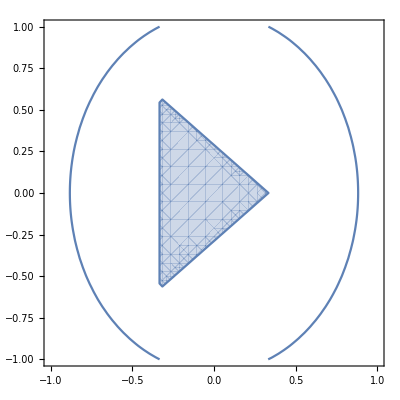

```mathematica
Show[positivereg,pureline]
```

```mathematica
(* no pure, symmetric Werner states exist... in fact no pure positive Werner state exist! *)
```

```mathematica
d0=N[√3+√30]/9
```

0.801031

```mathematica
a0=√(7-6 d0^2)/3
```

0.591617

```mathematica
a0=(1-2 √3 d0)/3
```

-0.591617

```mathematica
purerho=rho/.{a-> a0,b-> a0,c-> a0,d-> d0}
```

(-0.0968565 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.198952 | -0.147904+0.200258 ⅈ | 0 | -0.147904-0.200258 ⅈ | 0 | 0 | 0
0 | -0.147904-0.200258 ⅈ | 0.198952 | 0 | -0.147904+0.200258 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0.198952 | 0 | -0.147904-0.200258 ⅈ | -0.147904+0.200258 ⅈ | 0
0 | -0.147904+0.200258 ⅈ | -0.147904-0.200258 ⅈ | 0 | 0.198952 | 0 | 0 | 0
0 | 0 | 0 | -0.147904+0.200258 ⅈ | 0 | 0.198952 | -0.147904-0.200258 ⅈ | 0
0 | 0 | 0 | -0.147904-0.200258 ⅈ | 0 | -0.147904+0.200258 ⅈ | 0.198952 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0968565)

```mathematica
Eigenvalues[purerho]
```

{0.693713,0.693713,-0.0968565,-0.0968565,-0.0968565,-0.0968565,-1.21319×10^-16,-5.2675×10^-17}

```mathematica
Eigensystem[purerho]
```

(-0.443713 | -0.443713 | 0.346856 | 0.346856 | 0.346856 | 0.346856 | 0.25 | 0.25
{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.288675-0.5 ⅈ,0.+0. ⅈ,-0.288675+0.5 ⅈ,0.57735+0. ⅈ,0.+0. ⅈ} | {0.+0. ⅈ,-0.30033+0.493088 ⅈ,-0.276862-0.506637 ⅈ,9.70694×10^-17-7.31239×10^-17 ⅈ,0.577191+0.0135492 ⅈ,9.84375×10^-17+7.12716×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ} | {1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ} | {0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ} | {0.+0. ⅈ,-0.577191-0.0135492 ⅈ,-0.577191-0.0135492 ⅈ,-1.15895×10^-16+8.71597×10^-17 ⅈ,-0.577191-0.0135492 ⅈ,-1.17389×10^-16-8.51366×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ} | {0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.57735+3.22439×10^-16 ⅈ,0.+0. ⅈ,0.57735-5.17563×10^-16 ⅈ,0.57735+0. ⅈ,0.+0. ⅈ} | {0.+0. ⅈ,-0.276862-0.506637 ⅈ,-0.30033+0.493088 ⅈ,1.35655×10^-16-1.08728×10^-16 ⅈ,0.577191+0.0135492 ⅈ,1.43815×10^-16+9.76802×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ} | {0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.288675-0.5 ⅈ,0.+0. ⅈ,0.288675+0.5 ⅈ,-0.57735+0. ⅈ,0.+0. ⅈ})

```mathematica
(* -- Basic Matrices recurring Matrices in N Qubit Werner States -- *)
```

```mathematica
deltaMatrix=-Sum[KroneckerProduct[pf[[i+1]],pf[[i+1]]],{i,3}]
```

(-1 | 0 | 0 | 0
0 | 1 | -2 | 0
0 | -2 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
Eigenvalues[deltaMatrix]
```

{3,-1,-1,-1}

```mathematica
epsilonMatrix=Sum[LeviCivitaTensor[3][[i,j,k]]*KroneckerProduct[pf[[i+1]],pf[[j+1]],pf[[k+1]]],{i,3},{j,3},{k,3}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | -2 ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0 | 2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 2 ⅈ | 0
0 | 2 ⅈ | -2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 ⅈ | 0 | 0 | -2 ⅈ | 0
0 | 0 | 0 | -2 ⅈ | 0 | 2 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[epsilonMatrix]
```

{-2 √3,-2 √3,2 √3,2 √3,0,0,0,0}

```mathematica
epsilonMatrix/(2I)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixPower[deltaMatrix,2]
```

(1 | 0 | 0 | 0
0 | 5 | -4 | 0
0 | -4 | 5 | 0
0 | 0 | 0 | 1)

```mathematica
MatrixPower[epsilonMatrix,2]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | -4 | 0 | -4 | 0 | 0 | 0
0 | -4 | 8 | 0 | -4 | 0 | 0 | 0
0 | 0 | 0 | 8 | 0 | -4 | -4 | 0
0 | -4 | -4 | 0 | 8 | 0 | 0 | 0
0 | 0 | 0 | -4 | 0 | 8 | -4 | 0
0 | 0 | 0 | -4 | 0 | -4 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
N[Eigenvalues[rho/.{a->0,b->0,c->0,d->1/(2 √3)}]]
```

{0.25,0.25,0.125,0.125,0.125,0.125,0.,0.}

```mathematica
N[1/(2 √3)]
```

0.288675

```mathematica
(* Legendre product *)
```

```mathematica
pr=LegendreP[1,y]LegendreP[2,y]LegendreP[3,y]
```

1/4 y (3 y^2-1) (5 y^3-3 y)

```mathematica
Integrate[pr,{y,-1,1}]
```

6/35

```mathematica
Integrate[LegendreP[2,y]LegendreP[2,y],{y,-1,1}]
```

2/5

```mathematica
Maximize[{(3/8)(a^2+b^2+c^2+2 d^2)+1,a+b+c+2Sqrt[a^2+b^2+c^2-a c -a b-b c+3d^2]≤  1&&1+a+b+c≥ 0 },{a,b,c,d}]
```

```mathematica
1/8 (3 a^2+3 b^2+3 c^2+6 d^2+1)
```

```mathematica
(* ----------- PLOTS ---------- *)
```

```mathematica
ulim=1;llim=-1;op=1;
```

```mathematica
(* AxesArrows to signify axes in the plot *)
org={0,0,0};
(*AxesArrows=Graphics3D[{Arrow[{org,{0,0,0.5}}],Arrow[{org,{0,0.5,0}}],Arrow[{org,{0.5,0,0}}]}];*)
AxesArrows=Graphics3D[{Arrow[{org,0.9 ulim{1,1,1}}]}];
```

```mathematica
(* font size *) fs=20;
LabelPositions={{0.75,-0.08,0},{0.85,0.6,0},{.97,.97,0.5}};
CustomAxesLabels=Graphics3D[{Text[Style["a",fs],LabelPositions[[1]]],Text[Style["b",fs],LabelPositions[[2]]],Text[Style["c",fs],LabelPositions[[3]]]}];
```

```mathematica
viewVec
```

{3.25,-2.5,0.25}

```mathematica
(* Plots of a,b,c space for various d .... the two parts of the region, top and bottom*)
PlotPSurface[d_]:=Module[{positivityCap,positivityBase,purity},
positivityCap=ContourPlot3D[a+b+c+2Sqrt[a^2+b^2+c^2-a c -a b-b c+3d^2]== 1 ,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->10, MeshStyle->Opacity[op],ContourStyle->Directive[Opacity[op]],RegionFunction-> Function[{a,b,c },1+a+b+c≥ 0 ]];
positivityBase=ContourPlot3D[1+a+b+c== 0 ,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->10,MeshStyle->Opacity[op],ContourStyle->Directive[Opacity[op]],RegionFunction-> Function[{a,b,c }, a+b+c+2Sqrt[a^2+b^2+c^2-a c -a b-b c+3d^2]≤  1 ]];
purity=ContourPlot3D[1/8 (3 a^2+3 b^2+3 c^2+6 d^2+1)== 1/2 ,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->10,ContourStyle->Directive[Red,Opacity[0.2]],MeshStyle->Directive[Opacity[0.2]],Mesh-> 3];
Show[positivityCap,positivityBase,purity,ViewPoint->viewVec,TicksStyle->Directive[FontOpacity->0,FontSize->0]]
]
```

```mathematica
(* PlotPRegion[d_]:=RegionPlot3D[a+b+c+2Sqrt[a^2+b^2+c^2-a c -a b-b c+3d^2]≤  1 &&1+a+b+c≥ 0 ,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->100] *)
```

```mathematica
N3Space1=PlotPSurface[0]
```

-Graphics3D-

```mathematica
N3Space2=PlotPSurface[√3/6]
```

-Graphics3D-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx v1\N3Space2.pdf",N3Space2];
```

```mathematica
N3Space3=PlotPSurface[√3/4]
```

-Graphics3D-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx v1\N3Space3.pdf",N3Space3];
```

```mathematica
N3Space4=PlotPSurface[√3/3]
```

-Graphics3D-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx v1\N3Space4.pdf",N3Space4];
```

```mathematica
(* Werner, epsilon *)
N[1/√6]
```

0.408248

```mathematica
N[1/(2 √3)]
```

0.288675

```mathematica
N[1/4]
```

0.25

```mathematica
N[1/6]
```

0.166667

```mathematica
(* SHOW THE SOLELY TRIPARTITE CORRELATIONS CAN BE PRODUCED FROM BISEPARABLE STATES *)
```

```mathematica
(* Example 1, superdiagonal core 3rd order tensor *)
```

```mathematica
(* qubit 1 Bloch vectors - unnormalized. To normalize them divide by √3 *)
u={{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
(* verify they sum to zero, needed in separability construction *)
Total[u,1]
```

{0,0,0}

```mathematica
(* qubit 2-3 correlation matrices, the four Bell states (conveniently constructed using the same u vectors above 
... note that qubit 2 and 3 have zero Bloch vectors *)
M={IdentityMatrix[3],IdentityMatrix[3],IdentityMatrix[3],IdentityMatrix[3]};
Do[M[[i]]=-DiagonalMatrix[u[[i]]],{i,4}];
```

```mathematica
tab=Table[Outer[Times,M[[i]],u[[i]]],{i,4}]
```

((-1 | -1 | -1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
-1 | -1 | -1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
-1 | -1 | -1)
(-1 | 1 | 1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
1 | -1 | -1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | -1 | -1)
(-1 | 1 | -1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
1 | -1 | 1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
-1 | 1 | -1)
(-1 | -1 | 1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
-1 | -1 | 1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | 1 | -1))

```mathematica
(* divide by √3 to normalize u's and by 4, the weight in the separable combinations *)
Total[tab,1]/(4 √3)
```

({-1/(√3),0,0} | {0,0,0} | {0,0,0}
{0,0,0} | {0,-1/(√3),0} | {0,0,0}
{0,0,0} | {0,0,0} | {0,0,-1/(√3)})

```mathematica
(* i.e. a superdiagonal result ... clearly "solely" tripartite ... no big deal in fact *)
```

```mathematica
(* Example 2, simple Werner state, with core 3rd order = ϵ/4, i.e. Levi Civita Tensor. This turns out biseparable as we see below*)
```

```mathematica
(* qubit 1 Bloch vectors - normalized. *)
u2={{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}};
(* verify they sum to zero, needed in separability construction *)
Total[u2,1]
```

{0,0,0}

```mathematica
(* qubit 2-3 correlation matrices, four maximally entangled states, one is singlet and other three are unitary acting on Bell states 
... note that qubit 2 and 3 have zero Bloch vectors *)
M2={({{-1, 0, 0}, {0, -1, 0}, {0, 0, -1}}),({{-1, 0, 0}, {0, 0, 1}, {0, -1, 0}}),({{0, 0, -1}, {0, -1, 0}, {1, 0, 0}}),({{0, 1, 0}, {-1, 0, 0}, {0, 0, -1}} )};
```

```mathematica
tab2=Table[Outer[Times,M2[[i]],u2[[i]]],{i,4}]
```

((-1 | -1 | -1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
-1 | -1 | -1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
-1 | -1 | -1)
(-1 | 1 | 1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | -1 | -1) | (0 | 0 | 0
-1 | 1 | 1
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
1 | -1 | 1) | (0 | 0 | 0
1 | -1 | 1
0 | 0 | 0) | (-1 | 1 | -1
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
-1 | -1 | 1
0 | 0 | 0) | (1 | 1 | -1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | 1 | -1))

```mathematica
Total[tab2,1]
```

({-2,0,0} | {-1,-1,1} | {1,-1,1}
{1,1,-1} | {0,-2,0} | {1,-1,-1}
{-1,1,-1} | {-1,1,1} | {0,0,-2})

```mathematica
IdentityMatrix[4]
```

```mathematica
Eigenvalues[r2rho[({{1, 0, 0, 0}, {0, 1/3, 0, 0}, {0, 0, 1/3, 0}, {0, 0, 0, 1/3}})]]
```

{1/3,1/3,1/3,0}

```mathematica
Eigenvalues[r2rho[({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 1, 0, 0}, {-0, 0, -1, 0}})]]
```

{1,0,0,0}

```mathematica
Eigenvalues[r2rho[({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})]]
```

{1/2,1/2,0,0}

```mathematica
a=.501;Eigenvalues[r2rho[({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, a, 0, 0}, {-0, 0, -a, 0}})]]
```

{0.5005,0.25,0.25,-0.0005}

```mathematica
a=0.49;Eigenvalues[r2rho[({{1, 0, 0, 0}, {0, 0, a, 0}, {0, 0, 0, -a}, {0, 0, 0, 0}})]]
```

{0.495,0.25,0.25,0.005}

```mathematica
N[√3]
```

1.73205